# zFunction table creator.

Purpose: This worksheet produces a numeric table of the plasma dispersion function for use in kinetic full wave codes. The table contains both Z and Z’, and is on a logarithmic grid such that it is calculated for very large argument, meaning that a smooth transition to the analytic limit can be done within whatever code uses the table if you run off the end of the table. The output is a netCDF file in the directory specified below.

-0.0498562+0.0511338 ⅈ

-174.761+63.6327 ⅈ

0.+1.77245 ⅈ

0.+1.77245 ⅈ

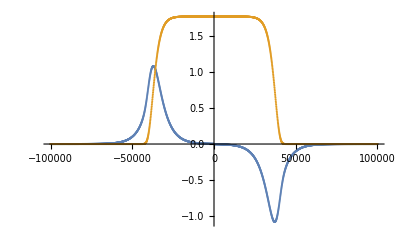

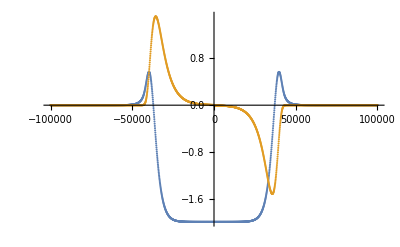

/Users/dg6/code/kineticj/mathematica

```mathematica
(*This form is from pg 406 is Swanson.*)
Z[re_,im_]:= I Sqrt[Pi] Exp[-(re+ I im)^2] Erfc[-I (re+I im)];
Zp[re_,im_]:=-2 (1+(re+I im) Z[re,im]);

(*This is the range and resolution of the file ... recall it's non-uniform resolution*)
argMin=0.001;argMax=100000;argN=1000;
zReNonUniform=N[Table[10^(i/(argN-1)*(Log10[argMax]-Log10[argMin])+Log10[argMin]),{i,0,argN-1}]];
zReNonUniform1=Prepend[zReNonUniform,0];
zReNonUniform2=Join[-Reverse[zReNonUniform],zReNonUniform1];
ZData=Z[zReNonUniform2,0];
ZPData=Zp[zReNonUniform2,0];

(*Print out a few values to check*)
Z[9.8,10.0]
Z[9.8,-10.0]
N[Z[0,0]]
N[I Sqrt[Pi]]

zReMin=-100000;zReMax=100000;nPtsRe=2000;
(*The above are only for the plotting range now. Use the lines above to specify the non-uniform file range. *)
ListPlot[{Re[ZData],Im[ZData]},DataRange->{zReMin,zReMax}]
ListPlot[{Re[ZPData],Im[ZPData]},DataRange->{zReMin,zReMax}]

(*Output file*)
SetDirectory["~/code/kineticj/mathematica"]
Export["zFunction.nc",{"arg_re"->zReNonUniform2, "Z_re"->Re[ZData], "Z_im"->Im[ZData], "Zp_re"->Re[ZPData],"Zp_im"->Im[ZPData]}];
```